# Analytical study of existence and stability limits in the absence of parasitoids

### Set at working directory

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/Quentin/Desktop/Article1/Tout_propre

## Model presentation

Four-stage pest model: eggs (U), larvae (L), nymphs (M), and adults (A). The variable H represents the integral of the mortality rate induced by larval competition.

```mathematica
ModelWithoutParasitoid = {
U'[t] == q  A[t] - q A[t-τu] Exp[-du τu]  - du U[t],
L'[t] == q  A[t-τu] Exp[-du τu]- q A[t-τu-τl] Exp[-du τu] H[t] -  (dl+c L[t]) L[t],
M'[t] == q  A[t-τu-τl] Exp[-du τu]H[t] -  q  A[t-τu-τl-τm] Exp[-du τu] H[t- τm]Exp[-dm τm] -  dm M[t],
A'[t] == q  A[t-τu-τl-τm] Exp[-du τu] H[t- τm]Exp[-dm τm] -da A[t],
H'[t] ==-c H[t](L[t]-L[t-τl])
};
```

All symbols follow Table 2. The egg density is denoted by U and the nymph density by M for compatibility with Mathematica.
H represents the proportion of larvae that survive the larval stage. This variable simplifies the computation of the survival integral. The same approach is used in the Julia code for numerical simulations.

## Analytical study

## Fixed points

Value of the larval survival proportion at equilibrium.

```mathematica
HeqNnTri = Exp[-τl (dl+c Leq)];
```

#### Model at equilibrium

```mathematica
modeleDdSsFxEq = { 
0== q  Aeq - q Aeq Exp[-du τu]  - du Ueq,
0==q  Aeq Exp[-du τu]- q  Aeq Exp[-du τu] HeqNnTri -  (dl+c Leq) Leq,
0==q  Aeq Exp[-du τu]HeqNnTri -  q  Aeq Exp[-du τu] HeqNnTri Exp[-dm τm] -  dm Meq,
0==q  Aeq Exp[-du τu]HeqNnTri Exp[-dm τm] -da Aeq
};
```

#### Solve the value of the variable at equilibrium

```mathematica
SolTot = Solve[modeleDdSsFxEq,{Ueq,Leq,Meq,Aeq}];
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is ⅇ^(du τu) Log[ⅇ^((dl+c Leq) τl)] (-dl τl+Log[ⅇ^((dl+c Leq) τl)]) == 0.

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is dm τm+du τu+Log[ⅇ^((dl+c Leq) τl)]+Log[da/q] == 0.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

#### Non-trivial value of densities at equilibrium

```mathematica
UeqNntri = Ueq/.SolTot[[3]][[1]]
LeqNnTri = Leq/.SolTot[[3]][[2]]
MeqNntri = Meq/.SolTot[[3]][[3]]
AeqNnTri = Aeq/.SolTot[[3]][[4]]
```

(ⅇ^(τl (dl+(-dl τl-dm τm-du τu-Log[da/q])/τl)) (-1+ⅇ^(du τu)) (dm τm+du τu+Log[da/q]) (dl τl+dm τm+du τu+Log[da/q]))/(c du (-1+ⅇ^(τl (dl+(-dl τl-dm τm-du τu-Log[da/q])/τl))) τl^2)

(-dl τl-dm τm-du τu-Log[da/q])/(c τl)

(da ⅇ^(du τu+τl (dl+(-dl τl-dm τm-du τu-Log[da/q])/τl)) (-1+ⅇ^(dm τm)) (dm τm+du τu+Log[da/q]) (dl τl+dm τm+du τu+Log[da/q]))/(c dm (-1+ⅇ^(τl (dl+(-dl τl-dm τm-du τu-Log[da/q])/τl))) q τl^2)

(ⅇ^(du τu+τl (dl+(-dl τl-dm τm-du τu-Log[da/q])/τl)) (dm τm+du τu+Log[da/q]) (dl τl+dm τm+du τu+Log[da/q]))/(c (-1+ⅇ^(τl (dl+(-dl τl-dm τm-du τu-Log[da/q])/τl))) q τl^2)

## Pest existence threshold

Condition for persistence in relation to the fertility rate

```mathematica
Solve [0==LeqNnTri,q,Reals]
```

{{q→da ⅇ^(dl τl+dm τm+du τu)}}

### Pest existence threshold (to be superimposed on Figure 2)

```mathematica
EqExThresholddu=Solve [0==LeqNnTri/.{τu-> 4,τl->16,τm->8,c->0.0001, dl->0,dm->0,da->0.1},du,Reals] [[1]][[1]]
Export["../table/Curve/EqExThresholdWithoutPara_du.txt",CForm[EqExThresholddu[[2]]],"Text"];
```

du→0.-0.25 Log[0.1/q]

```mathematica
EqExThresholddl=Solve [0==LeqNnTri/.{τu-> 4,τl->16,τm->8,c->0.0001, du->0,dm->0,da->0.1},dl,Reals]  [[1]][[1]]
Export["../table/Curve/EqExThresholdWithoutPara_dl.txt",CForm[EqExThresholddl[[2]]],"Text"];
```

dl→0.-0.0625 Log[0.1/q]

```mathematica
EqExThresholddm=Solve [0==LeqNnTri/.{τu-> 4,τl->16,τm->8,c->0.0001, du->0,dl->0,da->0.1},dm,Reals]  [[1]][[1]]
Export["../table/Curve/EqExThresholdWithoutPara_dm.txt",CForm[EqExThresholddm[[2]]],"Text"];
```

dm→0.-0.125 Log[0.1/q]

```mathematica
EqExThresholdda=Solve [0==LeqNnTri/.{τu-> 4,τl->16,τm->8,c->0.0001, du->0,dl->0,dm->0.1},da,Reals]  [[1]][[1]]
Export["../table/Curve/EqExThresholdWithoutPara_da.txt",CForm[EqExThresholdda[[2]]],"Text"];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

da→0.449329 q

## Linearization in the vicinity of a non-trivial fixed point

```mathematica
LinearModel = {
nL'[t] == q nA[t-τu] Exp[-du τu]- q nA[t-τu-τl] Exp[-du τu]  Heq -q Aeq Exp[-du τu]  Hn[t] -(dl+c nL[t]) Leq-(dl+c Leq) nL[t],
nA'[t] == q nA[t-τu-τl-τm] Exp[-du τu] Heq Exp[-dm τm]+q Aeq Exp[-du τu] nH[t- τm]Exp[-dm τm] -da nA[t],
nH'[t] ==-c Heq(nL[t]-nL[t-τl])
}
```

{nL'[t]==-Aeq ⅇ^(-du τu) q Hn[t]+ⅇ^(-du τu) q nA[t-τu]-ⅇ^(-du τu) Heq q nA[t-τl-τu]-(dl+c Leq) nL[t]-Leq (dl+c nL[t]),nA'[t]==-da nA[t]+ⅇ^(-dm τm-du τu) Heq q nA[t-τl-τm-τu]+Aeq ⅇ^(-dm τm-du τu) q nH[t-τm],nH'[t]==-c Heq (nL[t]-nL[t-τl])}

## Laplace transformation

```mathematica
LaplaceModel = {
-s L[s]+q A[s]Exp[-s τu] Exp[-du τu]- q A[s] Exp[-s(τu+τl)] Exp[-du τu]  Heq -q Aeq Exp[-du τu]  H[s] - dl L[s]-2 c Leq L[s],
-s A[s]+q A[s] Exp[-s(τu+τl+τm)] Exp[-du τu] Heq Exp[-dm τm]+q Aeq Exp[-du τu] H[s]Exp[- s τm]Exp[-dm τm] -da A[s],
-s H[s]-c Heq(L[s]-L[s]Exp[-s τl])
}
```

{ⅇ^(-du τu-s τu) q A[s]-ⅇ^(-du τu-s (τl+τu)) Heq q A[s]-Aeq ⅇ^(-du τu) q H[s]-dl L[s]-2 c Leq L[s]-s L[s],-da A[s]+ⅇ^(-dm τm-du τu-s (τl+τm+τu)) Heq q A[s]-s A[s]+Aeq ⅇ^(-dm τm-s τm-du τu) q H[s],-s H[s]-c Heq (L[s]-ⅇ^(-s τl) L[s])}

## Jacobian

```mathematica
GeneralJacobian =  D[LaplaceModel,{{L[s],A[s], H[s]}}];
MatrixForm[GeneralJacobian]
```

(-dl-2 c Leq-s | ⅇ^(-du τu-s τu) q-ⅇ^(-du τu-s (τl+τu)) Heq q | -Aeq ⅇ^(-du τu) q
0 | -da+ⅇ^(-dm τm-du τu-s (τl+τm+τu)) Heq q-s | Aeq ⅇ^(-dm τm-s τm-du τu) q
-c (1-ⅇ^(-s τl)) Heq | 0 | -s)

Calculation of the Jacobian for non-trivial equilibrium variable values

```mathematica
EqUntriJacobian = FullSimplify[GeneralJacobian/.{Leq->LeqNnTri,Aeq->AeqNnTri, Heq->(HeqNnTri/.Leq ->LeqNnTri)}]
```

{{(dl τl-s τl+2 dm τm+2 du τu+2 Log[da/q])/τl,ⅇ^(-s τu) (-da ⅇ^(-s τl+dm τm)+ⅇ^(-du τu) q),(q (dm τm+du τu+Log[da/q]) (dl τl+dm τm+du τu+Log[da/q]))/(c (da ⅇ^(dm τm+du τu)-q) τl^2)},{0,da (-1+ⅇ^(-s (τl+τm+τu)))-s,-(ⅇ^(-((dm+s) τm)) q (dm τm+du τu+Log[da/q]) (dl τl+dm τm+du τu+Log[da/q]))/(c (da ⅇ^(dm τm+du τu)-q) τl^2)},{-(c da ⅇ^(-s τl+dm τm+du τu) (-1+ⅇ^(s τl)))/q,0,-s}}

## Characteristic equation and its transformation

```mathematica
CharacteristicEquation = Det[EqUntriJacobian]
```

-((da (-1+ⅇ^(-s (τl+τm+τu)))-s) s (dl τl-s τl+2 dm τm+2 du τu+2 Log[da/q]))/τl-(c da ⅇ^(-s τl+dm τm+du τu) (-1+ⅇ^(s τl)) (-(ⅇ^(-((dm+s) τm)-s τu) q (-da ⅇ^(-s τl+dm τm)+ⅇ^(-du τu) q) (dm τm+du τu+Log[da/q]) (dl τl+dm τm+du τu+Log[da/q]))/(c (da ⅇ^(dm τm+du τu)-q) τl^2)-(q (da (-1+ⅇ^(-s (τl+τm+τu)))-s) (dm τm+du τu+Log[da/q]) (dl τl+dm τm+du τu+Log[da/q]))/(c (da ⅇ^(dm τm+du τu)-q) τl^2)))/q

```mathematica
D[CharacteristicEquation,c]
```

-(c da ⅇ^(-s τl+dm τm+du τu) (-1+ⅇ^(s τl)) ((ⅇ^(-((dm+s) τm)-s τu) q (-da ⅇ^(-s τl+dm τm)+ⅇ^(-du τu) q) (dm τm+du τu+Log[da/q]) (dl τl+dm τm+du τu+Log[da/q]))/(c^2 (da ⅇ^(dm τm+du τu)-q) τl^2)+(q (da (-1+ⅇ^(-s (τl+τm+τu)))-s) (dm τm+du τu+Log[da/q]) (dl τl+dm τm+du τu+Log[da/q]))/(c^2 (da ⅇ^(dm τm+du τu)-q) τl^2)))/q-(da ⅇ^(-s τl+dm τm+du τu) (-1+ⅇ^(s τl)) (-(ⅇ^(-((dm+s) τm)-s τu) q (-da ⅇ^(-s τl+dm τm)+ⅇ^(-du τu) q) (dm τm+du τu+Log[da/q]) (dl τl+dm τm+du τu+Log[da/q]))/(c (da ⅇ^(dm τm+du τu)-q) τl^2)-(q (da (-1+ⅇ^(-s (τl+τm+τu)))-s) (dm τm+du τu+Log[da/q]) (dl τl+dm τm+du τu+Log[da/q]))/(c (da ⅇ^(dm τm+du τu)-q) τl^2)))/q

We cannot solve this characteristic equation analytically to determine the stability of the non-trivial fixed points. However, we can search for parameter values at which the real part of the eigenvalues is zero, in order to identify the stability boundaries of the non-trivial fixed point.

### Focus on full imaginary solutions

```mathematica
CharacteristicEquationI =CharacteristicEquation /.{s->I x}
```

-(ⅈ (da (-1+ⅇ^(-ⅈ x (τl+τm+τu)))-ⅈ x) x (dl τl-ⅈ x τl+2 dm τm+2 du τu+2 Log[da/q]))/τl-(c da ⅇ^(-ⅈ x τl+dm τm+du τu) (-1+ⅇ^(ⅈ x τl)) (-(ⅇ^(-((dm+ⅈ x) τm)-ⅈ x τu) q (-da ⅇ^(-ⅈ x τl+dm τm)+ⅇ^(-du τu) q) (dm τm+du τu+Log[da/q]) (dl τl+dm τm+du τu+Log[da/q]))/(c (da ⅇ^(dm τm+du τu)-q) τl^2)-(q (da (-1+ⅇ^(-ⅈ x (τl+τm+τu)))-ⅈ x) (dm τm+du τu+Log[da/q]) (dl τl+dm τm+du τu+Log[da/q]))/(c (da ⅇ^(dm τm+du τu)-q) τl^2)))/q

```mathematica
eqCharaRe = ComplexExpand[Re[CharacteristicEquationI]];
eqCharaIm = ComplexExpand[Im[CharacteristicEquationI]];
```

## Numerical study

We numerically search for the stability boundaries of the model without parasitoids across each parameter space considered in the corresponding subfigures of Figure 2.

## Global parameters

```mathematica
τuN=4;τlN=16;τmN=8;cN=0.0001;duN=0;dlN=0;dmN=0;daN=0.1;
```

```mathematica
dMin =0.001; dMax = 1; dPas = 0.001;
qMin =0; qMax = 10; qPas = 0.01;

dRangeInv=Range[dMax,dMin,-dPas];
dRange=Range[dMin,dMax,dPas];
qRange=Range[qMin,qMax,qPas];
```

## stability limit as a function of da and q

### Parameterisation

```mathematica
eqCharaReEq = eqCharaRe /.{τu ->τuN,τl ->τlN,τm ->τmN,c ->cN,du ->duN,dl->dlN,dm->dmN};
eqCharaImEq = eqCharaIm /.{τu ->τuN,τl ->τlN,τm ->τmN,c ->cN,du ->duN,dl->dlN,dm->dmN};
```

```mathematica
D[eqCharaReEq,q];
D[eqCharaImEq,q] ;
```

### Search for initial values for FindR

```mathematica
FindRoot[{eqCharaReEq/.{da->0.2},eqCharaImEq/.{da->0.2}},{x,0.13},{q,70}]
FindRoot[{eqCharaReEq/.{da->0.2},eqCharaImEq/.{da->0.2}},{x,0.1},{q,1}]
```

{x→0.144706,q→12.2175}

{x→7.97324×10^-9,q→0.2}

### Creating curves

```mathematica
CourbeLimiteCompda = {}  ; 
ClearAll[qtempo, xtempo,da,q,root,  x]
qtempo =30;
xtempo =0.1;
Do [
root = FindRoot[{eqCharaReEq,eqCharaImEq},{x,xtempo},{q,qtempo}];
qtempo = q/.root ;
xtempo = x/.root ;
AppendTo[CourbeLimiteCompda,{qtempo,da}];
,{da,dMax,dMin,-dPas}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {x,q} = {0.0825637,1.24346×10^13}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

```mathematica
Export["../table/Curve/sansPara_LimiteStabDeltaA.csv",CourbeLimiteCompda,"CSV"]
```

../table/Curve/sansPara_LimiteStabDeltaA.csv

### Displaying curves

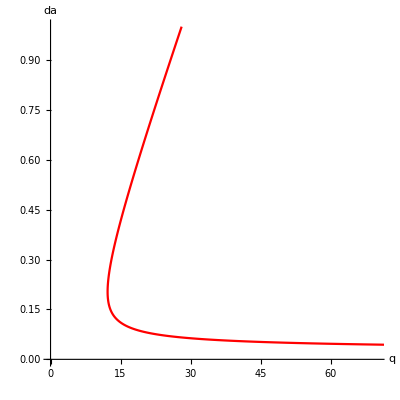

```mathematica
ListLinePlot[{CourbeLimiteCompda},
Axes->True,
AxesLabel -> {"q","da"},
PlotLegends -> Automatic,
Ticks->Automatic,
AxesOrigin->{0,0},
AspectRatio-> 1,
PlotRange->{{0,70},{0,1}},
Prolog->{},
PlotStyle->{Red}
]
```

## stability limit as a function of du and q

### Parameterisation

```mathematica
eqCharaReEq = eqCharaRe /.{τu ->τuN,τl ->τlN,τm ->τmN,c ->cN,da ->daN,dl->dlN,dm->dmN};
eqCharaImEq = eqCharaIm /.{τu ->τuN,τl ->τlN,τm ->τmN,c ->cN,da ->daN,dl->dlN,dm->dmN};
```

```mathematica
D[eqCharaReEq,q];
D[eqCharaImEq,q] ;
```

### Search for initial values for FindRoot

```mathematica
FindRoot[{eqCharaReEq/.{du->0.001},eqCharaImEq/.{du->0.001}},{x,0.1},{q,10}]
```

{x→0.125388,q→16.3708}

### Creating curves

```mathematica
CourbeLimiteCompdu = {}  ;

ClearAll[qtempo, xtempo,du,q,root,  x]
qtempo =20;
xtempo =0.12 ;
Do [
root = FindRoot[{eqCharaReEq,eqCharaImEq},{x,xtempo},{q,qtempo}];
qtempo = q/.root ;
xtempo = x/.root ;
AppendTo[CourbeLimiteCompdu,{qtempo,du}];
,{du,dMin,dMax,dPas}]
```

```mathematica
Export["../table/Curve/sansPara_LimiteStabDeltaU.csv",CourbeLimiteCompdu,"CSV"];
```

### Displaying curves

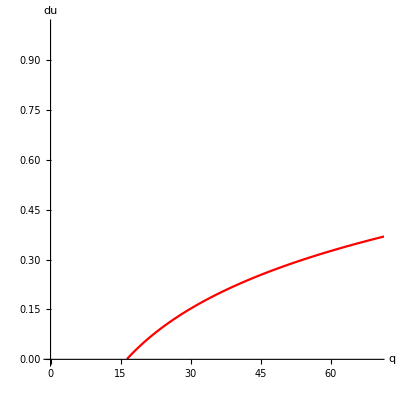

```mathematica
ListLinePlot[{CourbeLimiteCompdu},
Axes->True,
AxesLabel -> {"q","du"},
PlotLegends -> Automatic,
Ticks->Automatic,
AxesOrigin->{0,0},
AspectRatio-> 1,
PlotRange->{{0,70},{0,1}},
Prolog->{},
PlotStyle->{Red}
]
```

## Stability limit as a function of dl and q

### Parameterisation

```mathematica
eqCharaReEq = eqCharaRe /.{τu ->τuN,τl ->τlN,τm ->τmN,c ->cN,da ->daN,du->duN,dm->dmN};
eqCharaImEq = eqCharaIm /.{τu ->τuN,τl ->τlN,τm ->τmN,c ->cN,da ->daN,du->duN,dm->dmN};
```

```mathematica
D[eqCharaReEq,q];
D[eqCharaImEq,q] ;
```

### Search for initial values for FindR

```mathematica
FindRoot[{eqCharaReEq/.{dl->0.001},eqCharaImEq/.{dl->0.001}},{x,0.14},{q,20}]
```

{x→0.125392,q→16.4442}

### Creating curves

```mathematica
CourbeLimiteCompdl = {} ;

ClearAll[qtempo, xtempo,dl,q,root,  x]
qtempo =20;
xtempo =0.12 ;
Do [
root = FindRoot[{eqCharaReEq,eqCharaImEq},{x,xtempo},{q,qtempo}];
qtempo = q/.root ;
xtempo = x/.root ;
AppendTo[CourbeLimiteCompdl,{qtempo,dl}];
,{dl,dMin,dMax,dPas}]
```

```mathematica
Export["../table/Curve/sansPara_LimiteStabDeltaL.csv",CourbeLimiteCompdl,"CSV"];
```

### Displaying curves

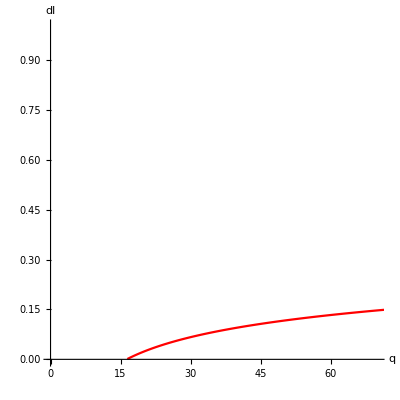

```mathematica
ListLinePlot[{CourbeLimiteCompdl},
Axes->True,
AxesLabel -> {"q","dl"},
PlotLegends -> Automatic,
Ticks->Automatic,
AxesOrigin->{0,0},
AspectRatio-> 1,
PlotRange->{{0,70},{0,1}},
Prolog->{},
PlotStyle->{Red}
]
```

## Stability limit as a function of dm and q

### Parameterisation

```mathematica
eqCharaReEq = eqCharaRe /.{τu ->τuN,τl ->τlN,τm ->τmN,c ->cN,da ->daN,du->duN,dl->dlN};
eqCharaImEq = eqCharaIm /.{τu ->τuN,τl ->τlN,τm ->τmN,c ->cN,da ->daN,du->duN,dl->dlN};
```

```mathematica
D[eqCharaReEq,q];
D[eqCharaImEq,q] ;
```

### Search for initial values for FindR

```mathematica
FindRoot[{eqCharaReEq/.{dm->0.001},eqCharaImEq/.{dm->0.001}},{x,0.14},{q,20}]
```

{x→0.125388,q→16.4364}

### Creating curves

```mathematica
CourbeLimiteCompdm = {} ;
ClearAll[qtempo, xtempo,dm,q,root,  x]
qtempo =16;
xtempo =0.1 ;
Do [
root = FindRoot[{eqCharaReEq,eqCharaImEq},{x,xtempo},{q,qtempo}];
qtempo = q/.root ;
xtempo = x/.root ;
AppendTo[CourbeLimiteCompdm,{qtempo,dm}];
,{dm,dMin,dMax,dPas}]
```

```mathematica
Export["../table/Curve/sansPara_LimiteStabDeltaM.csv",CourbeLimiteCompdm,"CSV"];
```

### Displaying curves

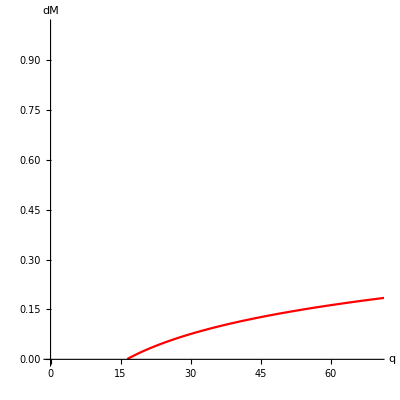

```mathematica
ListLinePlot[{CourbeLimiteCompdm},
Axes->True,
AxesLabel -> {"q","dM"},
PlotLegends -> Automatic,
Ticks->Automatic,
AxesOrigin->{0,0},
AspectRatio-> 1,
PlotRange->{{0,70},{0,1}},
Prolog->{},
PlotStyle->{Red}
]
```